```mathematica
SetDirectory[NotebookDirectory[]]
height=0.5;
length=4.0;
gap=2*Pi/length*3/2;
ks=2*gap;
M2=3;
M3=3;
ν1=2;
ν2=0.1;
g=980;
σ=72;
ρ=1;
```

/home/zack/oscillators/faraday

```mathematica
mat1[s_,k_,ω_,As_,ks_]:=ArrayFlatten[Table[Exp[-(k+n*ks)*height]*(-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+(k+n*ks)^2*ν2)-(g+σ/ρ*(k+n*ks)^2)*(k+n*ks))*KroneckerDelta[m,o]*(BesselJ[n-l,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l-1,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l+1,I*(k+n*ks)*As])+Exp[(k+n*ks)*height]*(-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+(k+n*ks)^2*ν2)+(g+σ/ρ*(k+n*ks)^2)*(k+n*ks))*KroneckerDelta[m,o]*(BesselJ[n-l,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l-1,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l+1,-I*(k+n*ks)*As]),{n,-M2,M2},{l,-M2,M2},{m,-M3,M3},{o,-M3,M3}]];
mat2[s_,k_,ω_,As_,ks_]:=ArrayFlatten[Table[Exp[-(k+n*ks)*height]*(ω^2*(k+n*ks)/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1])*(BesselJ[n-l,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l-1,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l+1,I*(k+n*ks)*As])+Exp[(k+n*ks)*height]*(-ω^2*(k+n*ks)/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1])*(BesselJ[n-l,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l-1,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l+1,-I*(k+n*ks)*As]),{n,-M2,M2},{l,-M2,M2},{m,-M3,M3},{o,-M3,M3}]]
```

{2.06614,Null}

{1.9362,Null}

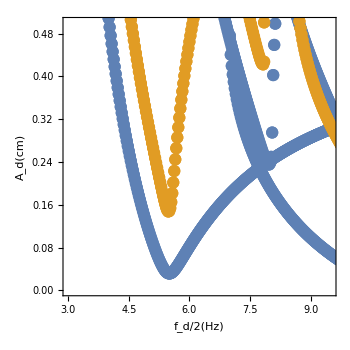

```mathematica
ω1=2*Pi*3;
ω2=2*Pi*20;
dω=2*Pi*0.05;AbsoluteTiming[vals1=DeleteCases[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.5,2*Pi/length,ω,0.0,ks],mat2[0.5,2*Pi/length,ω,0.0,ks]}],u_/;Abs[Im[u]]<10^-2]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]
AbsoluteTiming[vals2=DeleteCases[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.0,2*Pi/length,ω,0.0,ks],mat2[0.0,2*Pi/length,ω,0.0,ks]}],u_/;Abs[Im[u]]<10^-2]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]
p1=ListPlot[{Flatten[vals1,1],Flatten[vals2,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{3,9.5},{0,0.5}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350]
```

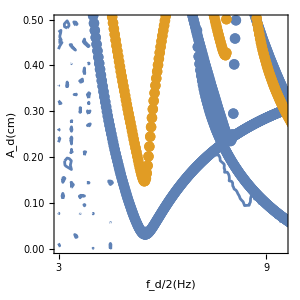

```mathematica
filebases={"sweeps/sharpamp/1001"};
cols={ColorData[97,"ColorList"][[1]]};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;p3=Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},PlotRange->{{3,9.5},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black], FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],{i,1,Length[sweeps]}];
Show[p3,p1]
```

{8.39551,Null}

{8.48816,Null}

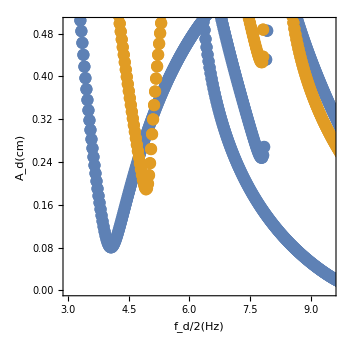

```mathematica
ω1=2*Pi*3;
ω2=2*Pi*20;
dω=2*Pi*0.05;AbsoluteTiming[vals3=DeleteCases[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.5,2*Pi/length,ω,0.4,ks],mat2[0.5,2*Pi/length,ω,0.4,ks]}],u_/;Abs[Im[u]]<10^-2]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]
AbsoluteTiming[vals4=DeleteCases[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.0,2*Pi/length,ω,0.4,ks],mat2[0.0,2*Pi/length,ω,0.4,ks]}],u_/;Abs[Im[u]]<10^-2]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]

p2=ListPlot[{Flatten[vals3,1],Flatten[vals4,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{3,9.5},{0,0.5}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350]
```

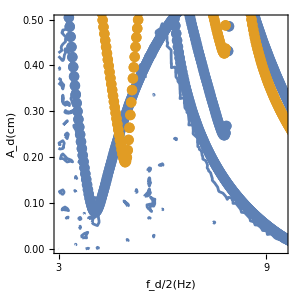

```mathematica
filebases={"sweeps/sharpamp/1003"};
cols={ColorData[97,"ColorList"][[1]]};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p3=Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},PlotRange->{{3,9.5},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black], FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],{i,1,Length[sweeps]}];
Show[p3,p2]
```

{1.64618,Null}

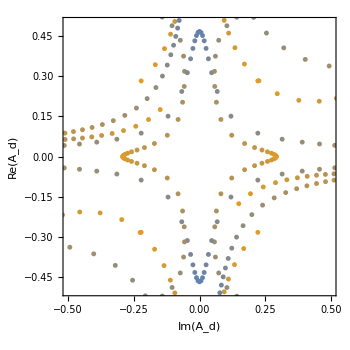

```mathematica
dϵ=0.02;
AbsoluteTiming[vals1=ParallelTable[val=Eigenvalues[{mat1[ϵ,2*Pi/length,2*Pi*12,0.4,ks],mat2[ϵ,2*Pi/length,2*Pi*12,0.4,ks]}];{Im[#],Re[#]}&/@val,{ϵ,0,1.0,dϵ}];]
cols=Blend[{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]},#]&/@(2*Abs[(Range[Length[vals1]]-(Length[vals1]-1)/2-1)/(Length[vals1]-1)]);
p1=ListPlot[vals1,Joined->False,PlotRange->{{-0.5,0.5},{-0.5,0.5}},PlotStyle->(Directive[#,PointSize[0.01]]&/@cols),ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]
```

{1.5308,Null}

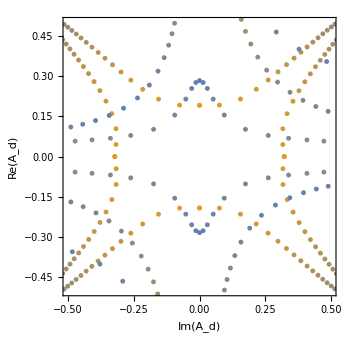

```mathematica
dϵ=0.02;
AbsoluteTiming[vals2=ParallelTable[val=Eigenvalues[{mat1[ϵ,2*Pi/length,2*Pi*9.8,0.4,ks],mat2[ϵ,2*Pi/length,2*Pi*9.8,0.4,ks]}];{Im[#],Re[#]}&/@val,{ϵ,0,1.0,dϵ}];]
cols=Blend[{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]},#]&/@(2*Abs[(Range[Length[vals1]]-(Length[vals1]-1)/2-1)/(Length[vals1]-1)]);
p2=ListPlot[vals2,Joined->False,PlotRange->{{-0.5,0.5},{-0.5,0.5}},PlotStyle->(Directive[#,PointSize[0.01]]&/@cols),ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]
```

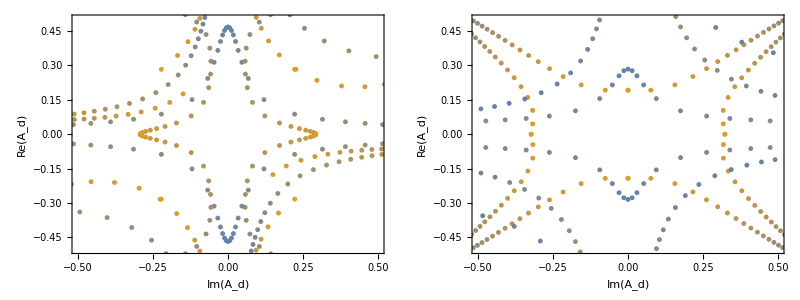

plots/eigenvalues.pdf

```mathematica
p=Grid[{{p1,p2}}]
Export["plots/eigenvalues.pdf",p]
```

{1.68331,Null}

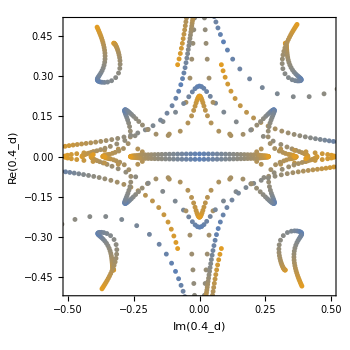

```mathematica
A=0.4;
f=20;AbsoluteTiming[vals2=ParallelTable[val=Eigenvalues[{mat1[ϵ,2*Pi/length,2*Pi*f,A,ks],mat2[ϵ,2*Pi/length,2*Pi*f,A,ks]}];{Im[#],Re[#]}&/@val,{ϵ,0,1.0,dϵ}];]
cols=Blend[{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]},#]&/@(2*Abs[(Range[Length[vals1]]-(Length[vals1]-1)/2-1)/(Length[vals1]-1)]);
p2=ListPlot[vals2,Joined->False,PlotRange->{{-0.5,0.5},{-0.5,0.5}},PlotStyle->(Directive[#,PointSize[0.01]]&/@cols),ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]
```

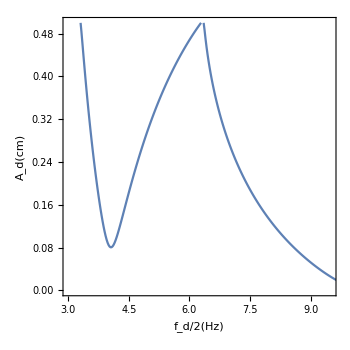

```mathematica
First@MinimalBy[#,#[[2]]&]&/@vals1;
ListPlot[First@MinimalBy[#,#[[2]]&]&/@vals1,Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->{{3,9.5},{0,0.5}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350]
```

```mathematica
Transpose[{vals3,vals4}]
```

Transpose::nmtx: The first two levels of {{{{1.95,7.85205},{1.95,7.85205}},{{1.975,7.62617},{1.975,7.62617}},{{2.,7.40883},{2.,7.40883}},«46»,{{3.225,4.95698},{3.225,4.95698},{3.225,3.80863},{3.225,3.80863},{3.225,0.711981},{3.225,0.711981},{3.225,0.552155},{3.225,0.552155}},«271»},{«1»}} cannot be transposed.

Transpose[{{{{1.95,7.85205},{1.95,7.85205}},319,{{10.,6.67937},{10.,6.67937},{10.,1.33565},{10.,1.33565},4,{10.,0.263773},{10.,0.263773},{10.,0.0100104},{10.,0.0100104}}},{1}}]
 |  |  |  |

```mathematica
AbsoluteTiming[vals5=DeleteCases[ParallelTable[val1=Abs[Cases[Eigenvalues[{mat1[0.0,2*Pi/length,ω,0.4,ks],mat2[0.0,2*Pi/length,ω,0.4,ks]}],u_/;Abs[Im[u]]<10^-2]];val2=Abs[Cases[Eigenvalues[{mat1[0.5,2*Pi/length,ω,0.4,ks],mat2[0.0,2*Pi/length,ω,0.4,ks]}],u_/;Abs[Im[u]]<10^-2]];
val=Join[val1,val2];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]
```

{16.6696,Null}

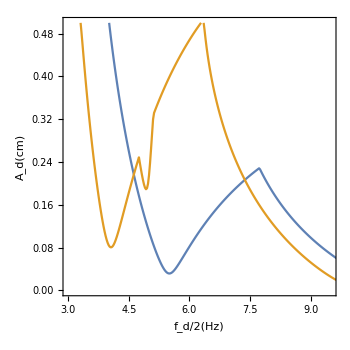

data/flatfloquet.txt

data/periodicfloquet.txt

```mathematica
ListPlot[{First@MinimalBy[#,#[[2]]&]&/@vals1,First@MinimalBy[#,#[[2]]&]&/@vals5},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->{{3,9.5},{0,0.5}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350]
Export["data/flatfloquet.txt",First@MinimalBy[#,#[[2]]&]&/@vals1,"Table"]
Export["data/periodicfloquet.txt",First@MinimalBy[#,#[[2]]&]&/@vals5,"Table"]
```